# Text Table Minimization Functions

## By Davey Morse

## Given a two dimensional list of text, these functions produce a minimized text table. The functions vary in their methods, precision, and timing, so the relevance of each is dependent on how the user comparatively values quality and speed.

## Notes: - could find the maximum number of characters in any word in a column and set the minimum possible width to the length of that word - note about the constraints: for relatively smaller tables, in the NMinimize function, the constraint that ensures the total table width is below the specified value needed to be lowered a little - there currently exists a lot of repetition, wish there was a better way for users to define functions

TextConstrict
Perfectly Optimizes the Dimensions of a Data Table
Only possible error coming from slight mismatch between the idealized continuity of text area and the actual word break intervals. Ideas for how to actually account for word breaks:

#### Non-Manipulable Version of Text-Constrict, where Output is TextGrid

```mathematica
TextConstrict[contents_List/; (*contents must be a list compatible with 2x2 table*)
 Depth[contents]==3, tablewidth_Real/;0<tablewidth<=1]:= 
Module[{ dimens,datatable,adjustablewidths,colwidths,height, solutions,col},
dimens = Dimensions[contents]; (*shorthand*)
adjustablewidths = Table[col[i],{i,dimens[[2]]-1}];(*list of adjustable parameters*)
colwidths = Append[adjustablewidths,Subtract[tablewidth,Total[adjustablewidths]]]; (*list of column widths, which are the above parameters as well as the final column width, which is the difference of the table width and the total of all of the other column widths*)
datatable = Table[StringLength[contents[[i,j]]],{i,dimens[[1]]},{j,dimens[[2]]}];
(*from the inputted list, makes parallel list storing the number of characters in each cell*)
height = Total[Map[Max,Table[StringLength[contents[[i,j]]]/colwidths[[j]],{i,dimens[[1]]},{j,dimens[[2]]}],2]]; (*the total height of the data table, written in terms of the given characternumbers per cell. equal to the  sum maximum of Area[cell ij]/(col j width) for all cells in a given row for each row*)
solutions  = Table[col[i]/.#, {i,dimens[[2]]-1}]&@NMinimize[{
height,Flatten[{0<Total[adjustablewidths]<tablewidth-.05,Table[col[i]>0,{i,dimens[[2]]-1}]}]},adjustablewidths,WorkingPrecision->10
][[2]]; (*finding the column widths that minimize the height of the datatable (which also, by extension, minimize the area*)
TextGrid[contents, Alignment->{Center},ItemSize->{Scaled/@(colwidths/.col[i_]:> solutions[[i]])},Frame->All] (*Text Grid with column widths as solutions*)
]
```

#### Manipulable Version of Text-Constrict, where Output is Manipulable TextGrid

```mathematica
TextConstrictManip[contents_List/;
 Depth[contents]==3, tablewidth_Real/;0<=tablewidth<=1]:= 
Module[{ dimens,datatable,adjustablewidths,colwidths,height, solutions,scaledSolutions,params, sizes,col},
dimens = Dimensions[contents]; (*shorthand*)
adjustablewidths = Table[col[i],{i,dimens[[2]]-1}];(*list of adjustable parameters*)
colwidths = Append[adjustablewidths,Subtract[tablewidth,Total[adjustablewidths]]]; (*list of column widths, which are the above parameters as well as the final column width, which is the difference of the table width and the total of all of the other column widths*)
datatable = Table[StringLength[contents[[i,j]]],{i,dimens[[1]]},{j,dimens[[2]]}];
(*from the inputted list, makes parallel list storing the number of characters in each cell*)
height = Total[Map[Max,Table[StringLength[contents[[i,j]]]/colwidths[[j]],{i,dimens[[1]]},{j,dimens[[2]]}],2]]; (*the total height of the data table, written in terms of the given characternumbers per cell. equal to the  sum maximum of Area[cell ij]/(col j width) for all cells in a given row for each row*)
solutions  = Table[Divide[col[i]/.#,1], {i,dimens[[2]]-1}]&@NMinimize[{
height,Flatten[{0<Total[adjustablewidths]<tablewidth-.05,Table[col[i]>0,{i,dimens[[2]]-1}]}]},adjustablewidths,WorkingPrecision->5,AccuracyGoal->5
][[2]]; (*finding the column widths that minimize the height of the datatable (which also, by extension, minimize the area*)
(*scaledSolutions = tablewidth*Rescale[solutions,{0,Total[solutions]}];*)
params=
Sequence@@
({#,.01,Min[1/(√2),.75],ControlPlacement-> Top}&/@Table[{adjustablewidths[[i]],solutions[[i]],StringJoin["Column " ,IntegerName[i]," width"]},{i,dimens[[2]]-1}]); (*Generates a list of the column width parameters for the manipulate function, which all begin at their optimal value, then can be adjusted by user to show that there is no better arrangement*)
sizes=Scaled/@colwidths; (*the scaled optimal width of each column*)
With[{$sizes=sizes,$params=params},
Manipulate[
TextGrid[contents, Alignment->{Center},ItemSize->{$sizes},Frame->All],$params
]
](*Creates a Manipulate allowing user to adjust column widths interactively to experiment with how different adjustments affect the total area of the table. The conclusion should be that there is no arrangment that better minimizes the table than the current one.*)
]
```

TextSqueeze
Approximating based on Average Column Width and Maximum Deviation

#### Non-Manipulable Version

```mathematica
TextSqueeze[contents_List/;
 Depth[contents]==3, tablewidth_Real/;0<=tablewidth<=1]:=
Module[
{ dimens,datatable, colmeans,meanDeviations,solutions,params, sizes,col,deviations},
dimens = Dimensions[contents]; (*shorthand for the dimensions of the dataset*)
datatable = Table[StringLength[contents[[i,j]]],{i,dimens[[1]]},{j,dimens[[2]]}]; (*recording the number of equal-width text characters in each cell*)
colmeans =Table[Total[Transpose[datatable][[i]]],{i,dimens[[2]]}]/dimens[[1]]; (*mean number of characters per cell in each column*)
deviations = Table[Transpose[datatable][[i]]/colmeans[[i]],{i,dimens[[2]]}]; (*deviation of number of character's in each cell from the average number of characters for that cell's column*)
meanDeviations = Mean/@Abs[deviations-1]; (*mean deviation of cells for each row; without absolute value, negative and positive directions of deviation cancel each other out*)
solutions = Table[(1+meanDeviations[[i]]) colmeans[[i]],{i,dimens[[2]]}]; (*multiplies the average deviation in a column by the width that would be established by TextSurround*)
TextGrid[contents, Alignment->{Center},ItemSize->{Scaled/@N[tablewidth*Rescale[solutions,{0,Total[solutions]}]]},Frame->All]
]
```

#### Manipulable Version

```mathematica
TextSqueezeManip[contents_List/;
 Depth[contents]==3, tablewidth_Real/;0<=tablewidth<=1]:=
Module[
{ dimens,datatable, adjustablewidths,colwidths,colmeans,meanDeviations,solutions,scaledSolutions, params, sizes,col,deviations},
dimens = Dimensions[contents]; (*shorthand for the dimensions of the dataset*)
datatable = Table[StringLength[contents[[i,j]]],{i,dimens[[1]]},{j,dimens[[2]]}]; (*recording the number of equal-width text characters in each cell*)
colmeans =Table[Total[Transpose[datatable][[i]]],{i,dimens[[2]]}]/dimens[[1]]; (*mean number of characters per cell in each column*)
deviations = Table[Transpose[datatable][[i]]/colmeans[[i]],{i,dimens[[2]]}]; (*deviation of number of character's in each cell from the average number of characters for that cell's column*)
meanDeviations = Mean/@Abs[deviations-1]; (*mean deviation of cells for each row; without absolute value, negative and positive directions of deviation cancel each other out*)
solutions = Table[(1+meanDeviations[[i]]) colmeans[[i]],{i,dimens[[2]]}]; (*multiplies the average deviation in a column by the width that would be established by TextSurround*)
scaledSolutions = N[tablewidth*Rescale[solutions,{0,Total[solutions]}]];
(*rescales solutions so that ratio among column widths is maintained, but now they sum to one. This characteristic is necessary for the later-used Scaled function, which interprets values as fractional widths on the screen, not as independent values*)
params=Sequence@@({#,.01,1/Sqrt[dimens[[2]]],ControlPlacement-> Top}&/@Table[{adjustablewidths[[i]],scaledSolutions[[i]],StringJoin["Column " ,IntegerName[i]]},{i,dimens[[2]]-1}]);
sizes=Scaled/@colwidths;
With[{$sizes=sizes,$params=params},
Manipulate[
TextGrid[contents, Alignment->{Center},ItemSize->{$sizes},Frame->All],$params
]
]
]
```

TextSurround
A simpler approximation

#### Non-Manipulable Version

```mathematica
TextSurround[contents_List/;
 Depth[contents]==3, tablewidth_Real/;0<=tablewidth<=1]:= 
Module[{ dimens,datatable,adjustablewidths,colwidths,colmeans,approxsolutions,col, solutions},
dimens = Dimensions[contents]; (*dimensions shorthand*)
datatable = Table[StringLength[contents[[i,j]]],{i,dimens[[1]]},{j,dimens[[2]]}]; (*the number of characters in each cell*)
colwidths = Append[#,Subtract[tablewidth,Total[#]]]&@Table[col[i],{i,dimens[[2]]-1}]; (*the parameters that determine the width of each column*)
colmeans =Table[Total[Transpose[datatable][[i]]],{i,dimens[[2]]}]; (*the total number of characters in each column*)
solutions  =tablewidth*N[Drop[colmeans,{dimens[[2]]}]/Total[colmeans]]; (*the relative ratios of each of the column's character counts to the total number of characters in the table*)
TextGrid[contents, Alignment->{Center},ItemSize->{Scaled/@(colwidths/.col[i_]:> solutions[[i]])},Frame->All]
]
```

#### Manipulable Version

```mathematica
TextSurroundManip[contents_List/;
 Depth[contents]==3, tablewidth_Real/;0<=tablewidth<=1]:= 
Module[{ dimens,datatable,adjustablewidths,colwidths,colmeans,approxsolutions,params, sizes,col, solutions},
dimens = Dimensions[contents]; (*dimensions shorthand*)
datatable = Table[StringLength[contents[[i,j]]],{i,dimens[[1]]},{j,dimens[[2]]}]; (*the number of characters in each cell*)
adjustablewidths = Table[col[i],{i,dimens[[2]]-1}];
colwidths = Append[#,Subtract[tablewidth,Total[#]]]&@adjustablewidths; (*the parameters that determine the width of each column*)
colmeans =Table[Total[Transpose[datatable][[i]]],{i,dimens[[2]]}]; (*the total number of characters in each column*)
solutions  =tablewidth*N[Drop[colmeans,{dimens[[2]]}]/Total[colmeans]]; (*the relative ratios of each of the column's character counts to the total number of characters in the table*)
params=Sequence@@({#,.01,2/Sqrt[dimens[[2]]],ControlPlacement-> Top}&/@Table[{adjustablewidths[[i]],solutions[[i]],StringJoin["Column " ,IntegerName[i]," width"]},{i,dimens[[2]]-1}]);
sizes=Scaled/@colwidths;
Column[{
With[{$sizes=sizes,$params=params},
Manipulate[
TextGrid[contents, Alignment->{Center},ItemSize->{$sizes},Frame->All],$params
]
]
}
]
]
```

Test Parameters

#### In order to generate random text:

```mathematica
characterconstant = 2; (*number of characters taken from sample text per unit area*)
thusfar[i_Integer, d_List]:=Total[Flatten[d][[1;;i]]]characterconstant+1; (*function allowing pull of text as according to a certain table of characternumbers in each cell*)
convertToList[spreadsheet_String]:=DeleteCases[DeleteCases[Import[spreadsheet],"",2],{},2];(*converts string indicating location of csv file into a compatible list*)

(*Generates a random list of tables of increasing size*)
generateAreas[r_Integer,c_Integer] := Table[RandomInteger[9]+1,r,c](*generates random table of areas that has r rows and c columns*)
tablelist = Table[generateAreas[i,i], {i,2,12}];
longtext = ExampleData[{"Text","AeneidEnglish"}];
contentslist = Partition[Table[StringTake[longtext,{thusfar[i-1, #] characterconstant,thusfar[i,#] characterconstant}],{i,Length[Flatten[#]]}],Dimensions[#][[1]]]&/@tablelist;
(*A single random table as well with specified dimensions; this one need not be a square table*)
datatable = Table[RandomInteger[RandomInteger[80]],5,3]; 

(*Excerpt of sample data*)
 Column[TextGrid[#,Frame-> All]&/@contentslist[[1;;3]]]
```

OOK I Arms, and the man I sin | ng, who, forc
c'd by fate, And haughty  |  Juno's unrel
OOK I Arms, and the man I sing, who, forc | c'd b | by fate, And haughty Juno
o's unrelenti | ing hate, | , Expell'd and exil'd, le
eft the Troja | an shore. Long labors, both b | by sea and land, he bore, And
OOK I Arms, and the man I sing, who, forc | c'd by fate, And haughty  |  Juno's unrelenting hate, Exp | pell'd and exil'd, left the Trojan sh
hore. Lon | ng labors, both b | by sea and land, he bore, And | d in the 
 doubtful war, before | e he won The Latian realm, and built  |  the destin'd town; His banis | sh'd gods restor'd to rites d
divine, And settled sure succession i | in his line, From whe | ence the race of Alban fathers come, And  |  the

#### List of Example Datasets

```mathematica
DOI = Partition[Table[StringTake[ExampleData[{"Text","DeclarationOfIndependence"}],{thusfar[i-1,datatable] characterconstant,thusfar[i,datatable] characterconstant}],{i,Length[Flatten[datatable]]}],Dimensions[datatable][[2]]]; (*Random table with strings in cells pulled from Dec of Independence*)
threebythree= convertToList["/Users/Davey/Downloads/threebythree.csv"]; (*Three by three table with lorem ipsum random text*)
titrationdata = convertToList["/Users/Davey/Downloads/titrationdatacsv.csv"]; (*data table used in a grade chem lab report*)
climatechangedata = convertToList["/Users/Davey/Downloads/ClimateChange.csv"];(*some random climate change data table*)
```

#### Testing

```mathematica
(*The following are each of my three functions, as well as the default TextGrid, applied to sample dataset
By comparing their heights (they all have the same width) one can evaluate how well they worked*)
```

```mathematica
Flatten[{#[DOI,1.]&/@{TextConstrict,TextSqueeze,TextSurround},TextGrid[DOI,Frame-> All]}]
```

{hen in the Course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the P | Powers of the earth, the separate and equal station to which the Laws of Nature and of Nature's God entitle them, a decent respect to the opinions of mankind requires that they should d | declare the causes which impel them to the separation. We hold these truths to be self-evident, that all men are created equal, that they are endowed by their Cr
reator with certain unalienable Rights, that amon | ng these are Life, Liberty, and the pursuit of Happiness.--That to secure these rights, Governments are instituted among Men, deriving their just powers from the consent of the governed,--That whenever any Form of Government becomes destructive of these ends, it is the | e Right o
of the People to alter or to abolish it, and to institute | e new Government, laying its foundation on such p | principles and organi
izing its powers in such form, as to them shall seem most likely to effect their Safety and Happiness. Prudence, indeed, will dic | ctate that Government | ts long established should not be changed for light a
and transient causes; and accordingly all experience hath shown, that mankind are more disposed to suffer, wh | hile evils are sufferable, than to right themselves by abolishing the forms to which they are accustomed. But when a long train of abuses and usurpations, pursuing invariably the same Object evinces a  |  design t,hen in the Course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the P | Powers of the earth, the separate and equal station to which the Laws of Nature and of Nature's God entitle them, a decent respect to the opinions of mankind requires that they should d | declare the causes which impel them to the separation. We hold these truths to be self-evident, that all men are created equal, that they are endowed by their Cr
reator with certain unalienable Rights, that amon | ng these are Life, Liberty, and the pursuit of Happiness.--That to secure these rights, Governments are instituted among Men, deriving their just powers from the consent of the governed,--That whenever any Form of Government becomes destructive of these ends, it is the | e Right o
of the People to alter or to abolish it, and to institute | e new Government, laying its foundation on such p | principles and organi
izing its powers in such form, as to them shall seem most likely to effect their Safety and Happiness. Prudence, indeed, will dic | ctate that Government | ts long established should not be changed for light a
and transient causes; and accordingly all experience hath shown, that mankind are more disposed to suffer, wh | hile evils are sufferable, than to right themselves by abolishing the forms to which they are accustomed. But when a long train of abuses and usurpations, pursuing invariably the same Object evinces a  |  design t,hen in the Course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the P | Powers of the earth, the separate and equal station to which the Laws of Nature and of Nature's God entitle them, a decent respect to the opinions of mankind requires that they should d | declare the causes which impel them to the separation. We hold these truths to be self-evident, that all men are created equal, that they are endowed by their Cr
reator with certain unalienable Rights, that amon | ng these are Life, Liberty, and the pursuit of Happiness.--That to secure these rights, Governments are instituted among Men, deriving their just powers from the consent of the governed,--That whenever any Form of Government becomes destructive of these ends, it is the | e Right o
of the People to alter or to abolish it, and to institute | e new Government, laying its foundation on such p | principles and organi
izing its powers in such form, as to them shall seem most likely to effect their Safety and Happiness. Prudence, indeed, will dic | ctate that Government | ts long established should not be changed for light a
and transient causes; and accordingly all experience hath shown, that mankind are more disposed to suffer, wh | hile evils are sufferable, than to right themselves by abolishing the forms to which they are accustomed. But when a long train of abuses and usurpations, pursuing invariably the same Object evinces a  |  design t,hen in the Course of human events, it becomes necessary for one people to dissolve the political bands which have connected them with another, and to assume, among the P | Powers of the earth, the separate and equal station to which the Laws of Nature and of Nature's God entitle them, a decent respect to the opinions of mankind requires that they should d | declare the causes which impel them to the separation. We hold these truths to be self-evident, that all men are created equal, that they are endowed by their Cr
reator with certain unalienable Rights, that amon | ng these are Life, Liberty, and the pursuit of Happiness.--That to secure these rights, Governments are instituted among Men, deriving their just powers from the consent of the governed,--That whenever any Form of Government becomes destructive of these ends, it is the | e Right o
of the People to alter or to abolish it, and to institute | e new Government, laying its foundation on such p | principles and organi
izing its powers in such form, as to them shall seem most likely to effect their Safety and Happiness. Prudence, indeed, will dic | ctate that Government | ts long established should not be changed for light a
and transient causes; and accordingly all experience hath shown, that mankind are more disposed to suffer, wh | hile evils are sufferable, than to right themselves by abolishing the forms to which they are accustomed. But when a long train of abuses and usurpations, pursuing invariably the same Object evinces a  |  design t}

## Accuracy Comparison

```mathematica
tableArea[f_, contents_, tablewidth_] :=Times@@Rasterize[f[contents,tablewidth],"BoundingBox"][[1;;2]]
```

```mathematica
tableAreaCompare[f_,g_,contents_,tablewidth_] := tableArea[f,contents, tablewidth]-tableArea[g,contents,tablewidth]
```

```mathematica
(*Comparing areas taken up by the tables*)
```

```mathematica
tableArea[#,contentslist[[4]],1.]&/@{TextConstrict,TextSqueeze,TextSurround}
```

{127650,148350,148479}

```mathematica
accuracies  = Quiet[Table[tableArea[function,#,1.]&/@contentslist,{function,{TextConstrict,TextSqueeze,TextSurround}}]]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

{{97835,143875,341847,475776,714771,953350,1436544,1693950,2192655,2975335,5065750},{97835,143750,341847,475363,714771,932650,1521792,1757577,2257111,3109641,3730391},{97835,144000,341550,497517,779227,997050,1583550,1887150,2348928,3314865,3970944}}

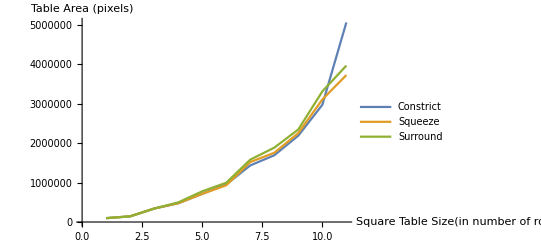

```mathematica
ListPlot[accuracies, Joined-> True, PlotLegends-> {"Constrict","Squeeze","Surround"},AxesLabel-> {"Square Table Size(in number of rows = number of columns)","Table Area (pixels)"}]
```

```mathematica
(*The percentage more area that textsqueeze produces in its tables*)
```

```mathematica
Mean[accuracies[[2]]/accuracies[[1]]-1]//N
```

-0.0105105

```mathematica
(*The percentage more area that textsurround produces in its tables*)
```

```mathematica
Mean[accuracies[[3]]/accuracies[[1]]-1]//N
```

0.0333967

```mathematica
(*Before weird deviation happens for TextConstrict (occurs circa number of rows in table is 11*)
Mean[accuracies[[2]][[1;;10]]/accuracies[[1]][[1;;10]]-1]//N
Mean[accuracies[[3]][[1;;10]]/accuracies[[1]][[1;;10]]-1]//N
```

0.014799

0.0583483

## Timing Comparison

```mathematica
timings = Quiet[Table[AbsoluteTiming[#[contentslist[[i]],1.]][[1]],{i,Length[contentslist]}]&/@{TextConstrict,TextSqueeze,TextSurround}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

{{0.16334,0.099066,2.2838,3.65399,6.12183,7.88255,8.19256,11.1765,11.8475,5.09199,2.91422},{0.000184,0.000143,0.000162,0.000221,0.000257,0.000341,0.000445,0.000456,0.000578,0.000877,0.000707},{0.00011,0.000123,0.000169,0.000156,0.000161,0.000235,0.000373,0.000266,0.000337,0.000343,0.000378}}

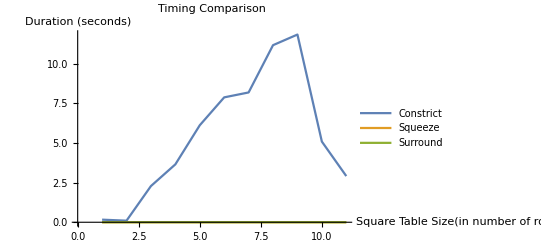

```mathematica
ListPlot[timings, Joined-> True, PlotLegends-> {"Constrict","Squeeze","Surround"},PlotLabel->"Timing Comparison",AxesLabel-> {"Square Table Size(in number of rows = number of columns)","Duration (seconds)"}]
```

As can be seen in above graph, weird drop occurs for the TextConstrict happens after number of rows/cols in table exceeds ten. Likely some sort of reduction in accuracy automated by NMinimize function that allows reduction in timing, as one can also see that quality of result produced by TextConstrict function (see plot above this one) is reduced tremendously at a the same table size.

```mathematica
Interpolation[timings[[1]]]
```

InterpolatingFunction[{{1., 11.}}, <>]